```mathematica
(*William Rodrigues*)
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.5 | 0. | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.5 | 0. | 0.5 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.5 | 0. | 0.5 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.5 | 0. | 0.5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.5 | 0. | 0.5 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.5 | 0. | 0.5 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0. | 0.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5 | 0. | 0.5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

{{20.,17.,14.,12.,10.,8.,6.,4.,2.,0.},{20.,17.,14.5,12.,10.,8.,6.,4.,2.,0.},{20.,17.25,14.5,12.25,10.,8.,6.,4.,2.,0.},{20.,17.25,14.75,12.25,10.125,8.,6.,4.,2.,0.},{20.,17.375,14.75,12.4375,10.125,8.0625,6.,4.,2.,0.},{20.,17.375,14.9063,12.4375,10.25,8.0625,6.03125,4.,2.,0.},{20.,17.4531,14.9063,12.5781,10.25,8.14063,6.03125,4.01563,2.,0.},{20.,17.4531,15.0156,12.5781,10.3594,8.14063,6.07813,4.01563,2.00781,0.},{20.,17.5078,15.0156,12.6875,10.3594,8.21875,6.07813,4.04297,2.00781,0.},{20.,17.5078,15.0977,12.6875,10.4531,8.21875,6.13086,4.04297,2.02148,0.}}

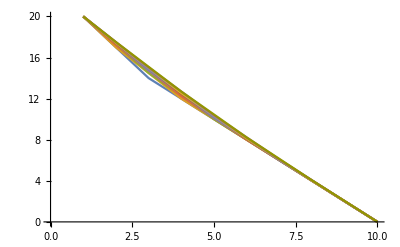

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.5 | 2. | -0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.5 | 2. | -0.5 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.5 | 2. | -0.5 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.5 | 2. | -0.5 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.5 | 2. | -0.5 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.5 | 2. | -0.5 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.5 | 2. | -0.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.5 | 2. | -0.5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

{{20.,15.,14.,12.,10.,8.,6.,4.,2.,0.},{20.,13.,14.5,12.,10.,8.,6.,4.,2.,0.},{20.,8.75,16.5,11.75,10.,8.,6.,4.,2.,0.},{20.,-0.75,22.75,10.25,10.125,8.,6.,4.,2.,0.},{20.,-22.875,40.75,4.0625,11.125,7.9375,6.,4.,2.,0.},{20.,-76.125,90.9063,-17.8125,16.25,7.3125,6.03125,4.,2.,0.},{20.,-207.703,228.781,-89.2031,37.75,3.48438,6.40625,3.98438,2.,0.},{20.,-539.797,606.016,-311.672,118.359,-15.1094,9.07813,3.76563,2.00781,0.},{20.,-1392.6,1637.77,-985.531,400.109,-93.9375,23.8281,1.98828,2.13281,0.},{20.,-3614.09,4464.6,-2990.,1339.95,-399.844,93.6309,-9.00391,3.27148,0.}}

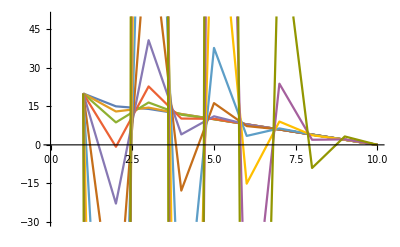

{{20.,17.,13.5,12.,10.,8.,6.,4.,2.,0.},{20.,16.25,14.75,11.25,10.125,8.,6.,4.,2.,0.},{20.,17.875,12.5938,13.1875,9.,8.3125,5.96875,4.,2.,0.},{20.,14.8281,17.5156,8.45313,12.3594,6.51563,6.57813,3.89063,2.00781,0.},{20.,21.6953,6.43359,20.3125,2.76563,12.5938,3.52539,5.01172,1.74414,0.},{20.,5.93164,33.0996,-9.5293,29.0337,-6.33691,14.7153,-0.384766,3.69434,0.},{20.,43.999,-32.4059,66.9993,-42.3368,49.396,-22.2614,20.1863,-4.98718,0.},{20.,-50.1555,132.785,-131.591,151.23,-111.093,92.5439,-49.6907,26.9984,0.},{20.,188.222,-290.947,390.123,-374.631,344.641,-251.612,172.161,-79.5763,0.},{20.,-425.533,812.477,-993.856,1057.72,-939.135,756.16,-503.429,254.958,0.}}

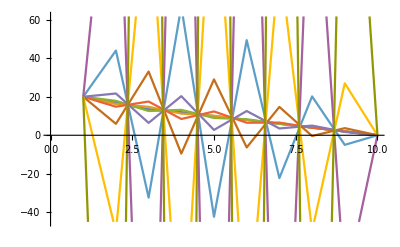

```mathematica
(*Foward*)

a=.5;
delx=.1;
delt=.01;
l=.5;
u={20,16,14,12,10,8,6,4,2,0};
FMatt={};
For[i=0,i<10,i++,
row={};
For[j=0,j<10,j++,
If[i==0&&j==0||i==9&&j==9,AppendTo[row,1],
If[i==0||i==9,AppendTo[row,0],
If[i==j,
AppendTo[row,1-2l],
If[i==j-1||j==i-1,
AppendTo[row,l],
AppendTo[row,0]
];
];
];
];
];
AppendTo[FMatt,row]
];
Print[MatrixForm[FMatt]]

un={};
n=10;
For[i=1,i≤n,i++,
var=FMatt.u;
u=var;
AppendTo[un,u];
];

Print[un]
ListLinePlot[un]

(*Backward*)

BMatt={};
For[i=0,i<10,i++,
row={};
For[j=0,j<10,j++,
If[i==0&&j==0||i==9&&j==9,AppendTo[row,1],
If[i==0||i==9,AppendTo[row,0],
If[i==j,
AppendTo[row,1+2l],
If[i==j-1||j==i-1,
AppendTo[row,-l],
AppendTo[row,0]
];
];
];
];
];
AppendTo[BMatt,row]
];
Print[MatrixForm[BMatt]]

u={20,16,14,12,10,8,6,4,2,0};
um={};
For[i=1,i≤n,i++,
var=BMatt.u;
u=var;
AppendTo[um,u];
];

Print[um]
ListLinePlot[um]

(*Crank*)
u={20,16,14,12,10,8,6,4,2,0};
uf={};
For[i=1,i≤n,i++,
var=BMatt.FMatt.u;
u=var;
AppendTo[uf,u];
];
Print[uf]
ListLinePlot[uf]
```